```mathematica
SetDirectory[NotebookDirectory[]];
```

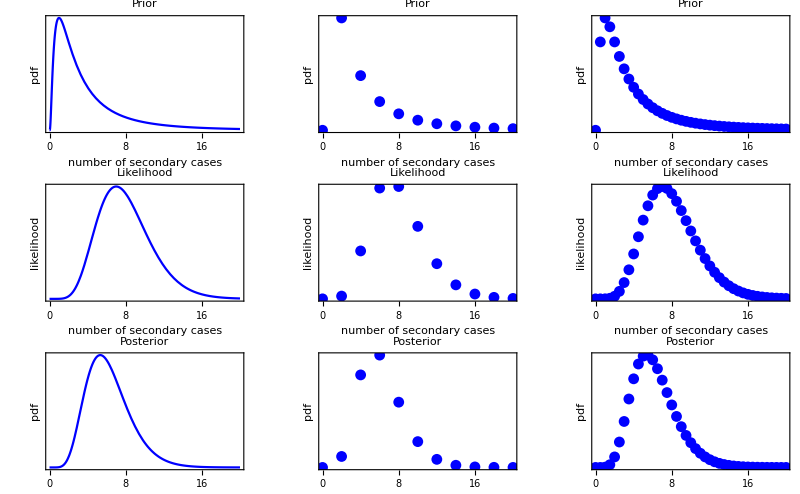

```mathematica
fPrior[λ_]:=PDF[LogNormalDistribution[1,1],λ]
data={7};
fLikelihood[λ_,lData__]:=Likelihood[PoissonDistribution[λ],lData]
aDenominator=NIntegrate[fLikelihood[λ,data]fPrior[λ],{λ,0,∞}];
fPosterior[λ_,lData_,aDenominator_]:=fLikelihood[λ,lData] fPrior[λ]/aDenominator
g1=Plot[fPrior[λ],{λ,0,20},PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"number of secondary cases","pdf"},BaseStyle->{FontSize->14},PlotStyle->Blue,PlotLabel->"Prior"];
g2=Plot[fLikelihood[λ,data],{λ,0,20},PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"number of secondary cases","likelihood"},BaseStyle->{FontSize->14},PlotStyle->Blue,PlotLabel->"Likelihood"];
g3=Plot[fPosterior[λ,data,aDenominator],{λ,0,20},PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"number of secondary cases","pdf"},BaseStyle->{FontSize->14},PlotStyle->Blue,PlotLabel->"Posterior"];
lPriorDiscrete = Table[fPrior[λ],{λ,0,20,2}];
lLikelihoodDiscrete =Table[If[i==0,0,fLikelihood[i,data]],{i,0,20,2}];
lPosteriorDiscrete=lPriorDiscrete lLikelihoodDiscrete;
lRange = Table[λ,{λ,0,20,2}];
lPriorDiscrete=Thread[{lRange,lPriorDiscrete}];
lLikelihoodDiscrete=Thread[{lRange,lLikelihoodDiscrete}];
lPosteriorDiscrete=Thread[{lRange,lPosteriorDiscrete}];
g1a=ListPlot[lPriorDiscrete,PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"number of secondary cases","pdf"},BaseStyle->{FontSize->14},PlotStyle->Blue,PlotLabel->"Prior"];
g2a=ListPlot[lLikelihoodDiscrete,PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"number of secondary cases","likelihood"},BaseStyle->{FontSize->14},PlotStyle->Blue,PlotLabel->"Likelihood"];
g3a=ListPlot[lPosteriorDiscrete,PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"number of secondary cases","pdf"},BaseStyle->{FontSize->14},PlotStyle->Blue,PlotLabel->"Posterior"];
lPriorDiscrete = Table[fPrior[λ],{λ,0,20,0.5}];
lLikelihoodDiscrete =Table[If[i==0,0,fLikelihood[i,data]],{i,0,20,0.5}];
lPosteriorDiscrete=lPriorDiscrete lLikelihoodDiscrete;
lRange = Table[λ,{λ,0,20,0.5}];
lPriorDiscrete=Thread[{lRange,lPriorDiscrete}];
lLikelihoodDiscrete=Thread[{lRange,lLikelihoodDiscrete}];
lPosteriorDiscrete=Thread[{lRange,lPosteriorDiscrete}];
g1b=ListPlot[lPriorDiscrete,PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"number of secondary cases","pdf"},BaseStyle->{FontSize->14},PlotStyle->Blue,PlotLabel->"Prior"];
g2b=ListPlot[lLikelihoodDiscrete,PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"number of secondary cases","likelihood"},BaseStyle->{FontSize->14},PlotStyle->Blue,PlotLabel->"Likelihood"];
g3b=ListPlot[lPosteriorDiscrete,PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"number of secondary cases","pdf"},BaseStyle->{FontSize->14},PlotStyle->Blue,PlotLabel->"Posterior"];
gFinal=Show[GraphicsGrid[{{g1,g1a,g1b},{g2,g2a,g2b},{g3,g3a,g3b}}],ImageSize->800]
```

```mathematica
Export["MCMC_discreteApproxBSE.pdf",gFinal]
```

MCMC_discreteApproxBSE.pdf

```mathematica
lTab=Table[If[λ==0,0,fLikelihood[λ,data]],{λ,0,20,2}];
N@(lTab)
```

{0.,0.00343709,0.0595404,0.137677,0.139587,0.0900792,0.0436822,0.0173917,0.00599374,0.00185002,0.000523468}

```mathematica
N@Total@lTab
```

0.499761